```mathematica
(*問題１*)
RandomInteger[{1,100},50]
Union[%]
Select[%,PrimeQ]
Length[%]
(* Lengthを使って、個数と同じ数字を求められるけど、
カウントと言えば今考えるのはFor文の形のものです*)
```

{57,66,93,92,11,63,73,43,38,100,99,36,29,75,35,83,17,26,68,65,57,62,56,44,25,88,42,69,46,99,33,85,24,50,97,63,18,14,100,55,76,64,89,40,2,12,48,11,83,3}

{2,3,11,12,14,17,18,24,25,26,29,33,35,36,38,40,42,43,44,46,48,50,55,56,57,62,63,64,65,66,68,69,73,75,76,83,85,88,89,92,93,97,99,100}

{2,3,11,17,29,43,73,83,89,97}

10

```mathematica
Clear["Global`*"]
```

```mathematica
(*問題2*)
```

```mathematica
a={1,2,3,4,5,6};
b={1,-1,1,-1,1,-1};
Table[a.RotateLeft[b,k],{k,0,5}]
```

{-3,3,-3,3,-3,3}

```mathematica
Clear["Global`*"]
```

```mathematica
(*問題3*)
f=x/(Exp[x]-1);
a=Normal[Series[f,{x,0,10}]];
b=CoefficientList[a,x];
```

```mathematica
c=b Table[n!,{n,0,10}]
```

{1,-1/2,1/6,0,-1/30,0,1/42,0,-1/30,0,5/66}

Thread::tdlen: {f} {1,1,2,6,24,120,720,5040,40320,362880,«1»}の長さが異なるオブジェクトは結合することができません．

```mathematica
(*検算*)
Clear["Global`*"]
```

```mathematica
Table[BernoulliB[x],{x,0,10}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
(*問題4*)
PolyhedronData[20]
```

```mathematica
{{"Antiprism",9},"ElongatedTriangularGyrobicupola","ElongatedTriangularOrthobicupola","GreatIcosahedron","GyroelongatedTriangularCupola","Icosahedron","JabulaniPolyhedron","JessensOrthogonalIcosahedron","MetabiaugmentedDodecahedron","ParabiaugmentedDodecahedron","RhombicIcosahedron","TetrahedronFiveCompound","TriangularHebesphenorotunda"}
```

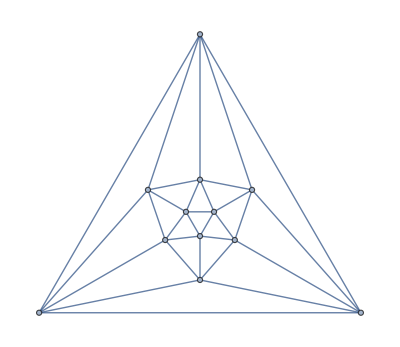

```mathematica
PolyhedronData["Icosahedron","Skeleton"]
```